```mathematica
l = {1,-1};
u={1,1};

f[0,l_] := {0,3}
f[n_, l_] := f[n-1,l] + l[[n]]

coords[l_] := f[#,l] & /@ Range[0,7]

plot[l_]:=ListPlot[{coords[l]},{Joined -> True, PlotRange->{-2,6}}]
plotall[l_] := Map[plot, l]


noperm = {l,l,l,l,u,u,u};
perms = Permutations[noperm];
plots = plotall[perms];
Manipulate[Show[plots[[x]]],{x,1,Length[plots],1}]
```

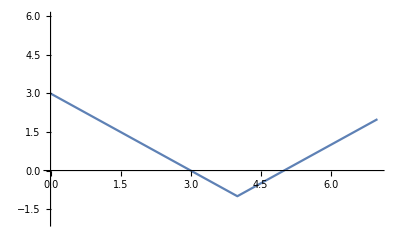
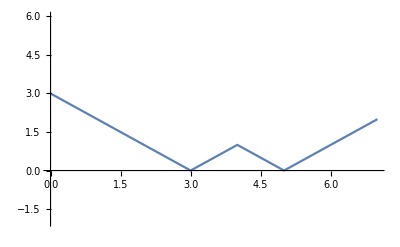
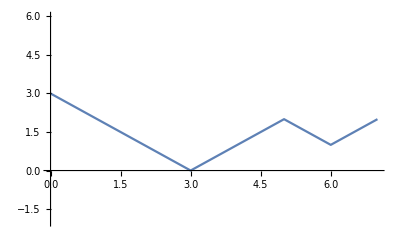
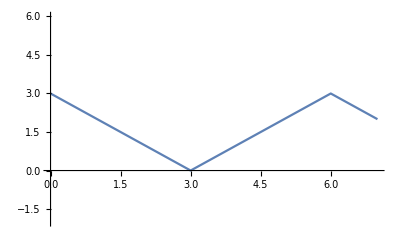
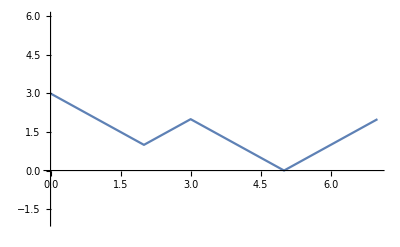
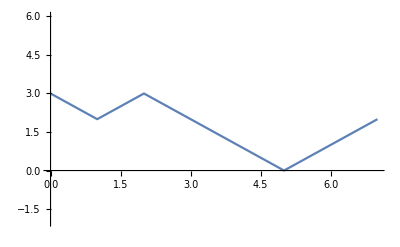
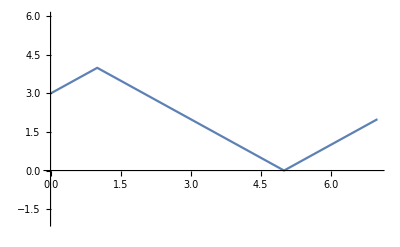

```mathematica
b1 = Permutations[{l,l,l,l,u}];
b1= Join[#,{u,u}]& /@ b1;
b2 = Permutations[{l,u,u,u}];
b2 = Join[{l,l,l},#]&/@b2;
b = Union[b1,b2];
plotall[b]
```

c

```mathematica
Binomial[25,10]
Binomial [25,5]
```

3268760

53130